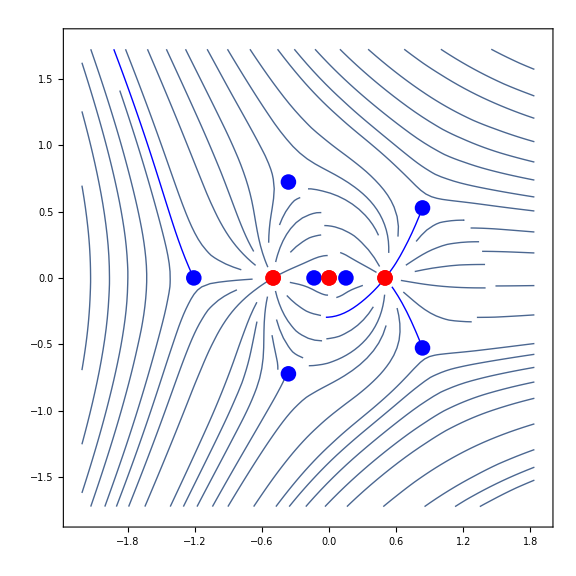
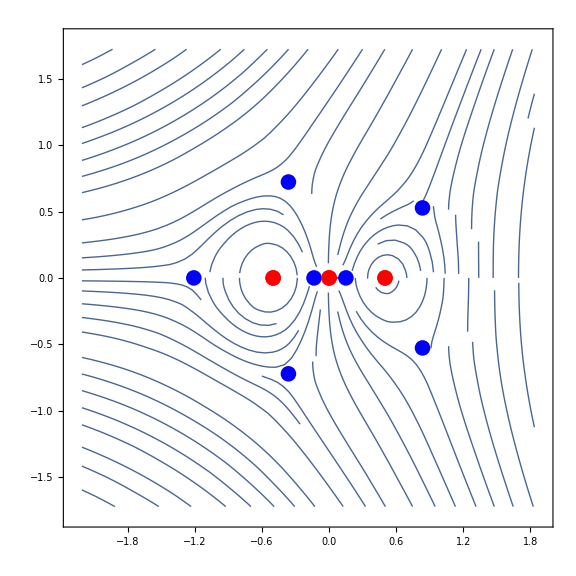

```mathematica
β=0.5;δ=0.5;
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
StokesGraph[potential,1]
Clear[β,δ,potential];
```

{-0.908562,0.454281+0.786834 ⅈ,0.454281-0.786834 ⅈ,-1.64355×10^-11+0.00185216 ⅈ,-1.64355×10^-11-0.00185216 ⅈ,0.000311717,-0.000311717}

-4.85051-0.45345 ⅈ

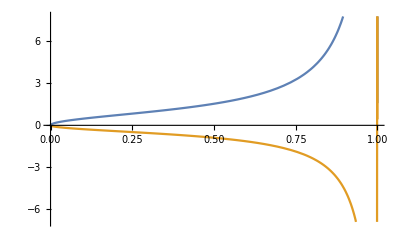
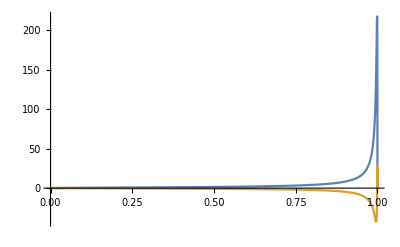

```mathematica
δ=0.001;β=0.001;
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦3⟧;
b=zeros⟦5⟧;

f=Function[t,potential[line[a,b][t]]];
chunks=sqrt[f,{t,0,10^-10,1-10^-10,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (a-b)(*√f[t]*)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,a,b,f,zeros,chunks,sqrtf,potential];
```

{-0.908562,0.454281+0.786834 ⅈ,0.454281-0.786834 ⅈ,-1.64355×10^-11+0.00185216 ⅈ,-1.64355×10^-11-0.00185216 ⅈ,0.000311717,-0.000311717}

4.85052-1.36035 ⅈ

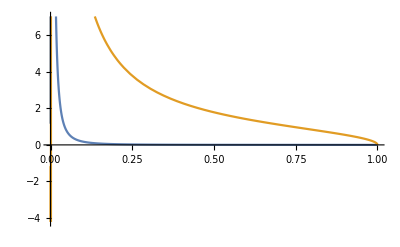
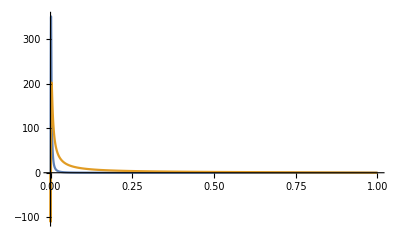

```mathematica
δ=0.001;β=0.001;
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

b=zeros⟦5⟧;
c=zeros⟦1⟧;

f=Function[t,potential[line[b,c][t]]];
chunks=sqrt[f,{t,0,10^-10,1-10^-10,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (b-c)(*√f[t]*)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,b,c,f,zeros,chunks,sqrtf,potential];
```

```mathematica
(*Constructing ab and bc functions*)
δbegining=-2;δend=2;δnstep=10;
βbegining=10^-2;βend=1;βnstep=10;
abList={};bcList={};
potential=Function[{x,δ,β},1/(4 (x^3-x β^2)^2)(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))];
ProgressIndicator[Dynamic[(β-βbegining)/(βend-βbegining)]]
For[β=βbegining,β<βend,β+=(βend-βbegining)/βnstep,
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,

zeros=NSolve[potential[z,δ,β]==0,z]//Quiet;

a=z/.zeros⟦3⟧;
b=z/.zeros⟦5⟧;
c=z/.zeros⟦1⟧;

f=Function[t,potential[line[a,b][t],δ,β]];
chunks=sqrt[f,{t,0,10^-10,1-10^-10,1}];
sqrtAB=Function[t,chunks];
ab=NIntegrate[-ⅈ (a-b)sqrtAB[t],{t,0,1}];
AppendTo[abList,{{δ,β},ab}];

f=Function[t,potential[line[b,c][t],δ,β]];
chunks=sqrt[f,{t,0,10^-10,1-10^-10,1}];
sqrtBC=Function[t,chunks];
bc=NIntegrate[-ⅈ (b-c)sqrtBC[t],{t,0,1}];
AppendTo[bcList,{{δ,β},bc}];

];
];

abFunc=Interpolation[abList];
bcFunc=Interpolation[bcList];
Clear[δ,β,a,b,c,ab,bc,sqrtAB,sqrtBC,f,chunks,potential,zeros,abList,bcList];
```

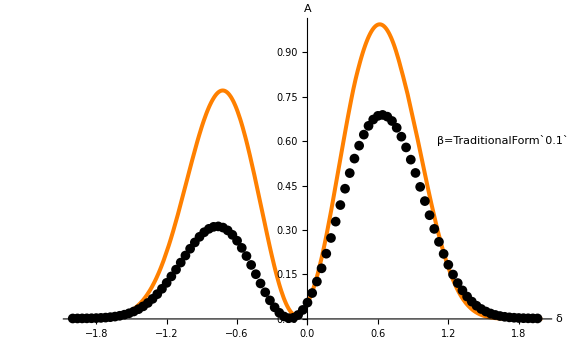

```mathematica
Dissipation={};
begining=-2;end=2;nstep=300;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]
β=0.1;

For[δ=begining,δ<end,δ+=(end-begining)/nstep,
R=ⅇ^(-2 (abFunc[δ,β]+bcFunc[δ,β])) Subscript[s, 1]+ⅇ^(-2 bcFunc[δ,β]) Subscript[s, 2]+Subscript[s, 3]/.{Subscript[s, 1]->-1.8ⅈ,Subscript[s, 2]->0,Subscript[s, 3]->-ⅈ}//Quiet;
Dissipation=Append[Dissipation,{δ,1-Abs[R]^2}];
]; 
Clear[R,δ,β(*,a,b,c,ab,bc,sqrtAB,sqrtBC,f,chunks,potential,zeros*)];
(*ListPlot[Dissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"},ImageSize->Large] *)
Show[Plot[Interpolation[Dissipation][x],{x,-2,2},PlotRange->Full,
AxesLabel->{Style["δ",FontSize->40,Black],Style["A",FontSize->40,Black]},
ImageSize->Large,
LabelStyle->{FontSize->20},
PlotStyle->{Orange,Thickness[0.005]}](*,lowField*)]
```

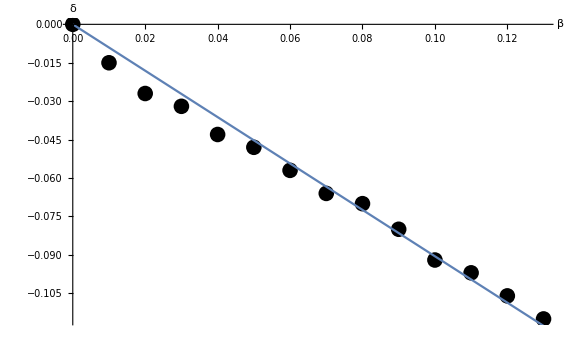

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/others/experiments/exersices/results/eta/zeroDissipationFromAnisortopism[Stokes].csv

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/others/experiments/exersices/results/eta/zeroDissipationFromAnisortopism[Stokes].png

```mathematica
βδStokesMinimum={{0,0},{0.01,-0.015},{0.02,-0.027},{0.03,-0.032},{0.04,-0.043},{0.05,-0.048},{0.06,-0.057},{0.07,-0.066},{0.08,-0.07},{0.09,-0.08},{0.1,-0.092},{0.11,-0.097},{0.12,-0.106},{0.13,-0.115}};

experiment=ListPlot[βδStokesMinimum,PlotRange->Full,AxesLabel->{β,δ},PlotStyle->Black];
fittingFunction=Function[β,a*β];
fit=FindFit[βδStokesMinimum,fittingFunction[β],a,β];
theory=Plot[fittingFunction[β]/.fit,{β,0,0.13},PlotRange->Full,PlotLegends->ToString[fittingFunction[β]/.fit,TraditionalForm]];

result=Show[{experiment,theory},ImageSize->Large]

SaveData["results/eta/zeroDissipationFromAnisortopism[Stokes].csv",βδStokesMinimum,"CSV"]
SaveData["results/eta/zeroDissipationFromAnisortopism[Stokes].png",result,"PNG"]
Clear[experiment,theory,fittingFunction,fit,result];
```

```mathematica
(*
 *
*
*
*
*
*
*
*
*
* Stokes analysis for electrical field; not working; just a memory; RIP!
*
*
*
*
*
*
*
*
*
 *)
```

```mathematica
(*β=0.4;δ=0.5;
potential=Function[x,1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))];
StokesGraph[potential,0.5]
Clear[β,δ,potential];*)
```

```mathematica
(*β=0.1;δ=1.1;
potential=Function[x,1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))];
zeros=NSolve[potential[z]==0,z];
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦2⟧;
c=zeros⟦1⟧;

f=Function[t,potential[line[a,c][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (a-c)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,a,c,f,zeros,chunks,sqrtf,potential];*)
```

```mathematica
(*Dissipation={};
begining=-1;end=1;nstep=100;β=0.1;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]

For[δ=begining,δ≤end,δ+=(end-begining)/nstep,
potential=Function[x,1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];

a=If[Length[zeros]>3,zeros⟦2⟧,zeros⟦1⟧];
(*b=-δ^2;*)
c=zeros⟦1⟧;

f=Function[t,potential[line[a,c][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

ac=If[a==c,0,NIntegrate[-ⅈ (a-c)sqrtf[t],{t,0,1}]];
(*bc=NIntegrate[-ⅈ (b-c)√(potential[s]/.s->line[b,c][t]),{t,0,1}];*)

R=ⅇ^(-2 (ac)) Subscript[s, 1]+ⅇ^(-2 bc) Subscript[s, 2]+Subscript[s, 3]/.{Subscript[s, 1]->ⅈ,Subscript[s, 2]->0,Subscript[s, 3]->ⅈ};
Dissipation=Append[Dissipation,{δ,1-Abs[R]^2}];
]; 
Clear[R,δ,β,a,b,c,ac,bc,zeros,f,chunks,sqrtf,potential];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"}]*)
```

```mathematica
b=Function[x,-(x+δ^2-β^2/x-(2β δ)/(x^2-β^2))];
z=Function[x,x^2/2-β^2 Log[x]];
Limit[Integrate[(-Im[b[x]/z'[x]^2]z'[x] ⅈ x/.x->-β+ρ ⅇ^(ⅈ ϕ)//ComplexExpand),{ϕ,-π,0}],ρ->0]
```

DirectedInfinity[-ⅈ Sign[δ (-19+20 β δ)]]

```mathematica
-(x ((x^2-β^2)^2-2 x β δ+x (x-β) (x+β) δ^2))/((x^2-β^2)^3)/.x->-β+ρ ⅇ^(ⅈ ϕ)//ComplexExpand
```

```mathematica
Series[1/(ρ^3 (4 β^2+ρ^2-4 β ρ Cos[ϕ])^3)(ρ^2 (8 β^4 (4 β^2+2 δ-5 β δ^2)+8 β^3 (7 β-5 δ^2) ρ^2+6 β (3 β-δ^2) ρ^4+ρ^6) Sin[ϕ]+ρ (16 β^5 δ (-2+β δ)-12 β^3 (4 β^2+2 δ-5 β δ^2) ρ^2+8 β^2 (-5 β+3 δ^2) ρ^4+(-5 β+δ^2) ρ^6) Sin[2 ϕ]+β (2 (8 β^5 δ-12 β^3 δ (-2+β δ) ρ^2+3 β (4 β^2+2 δ-5 β δ^2) ρ^4+2 (2 β-δ^2) ρ^6) Sin[3 ϕ]+ρ (-(24 β^4 δ-12 β^2 δ (-2+β δ) ρ^2+(4 β^2+2 δ-5 β δ^2) ρ^4) Sin[4 ϕ]+2 β δ ρ ((6 β^2+(2-β δ) ρ^2) Sin[5 ϕ]-β ρ Sin[6 ϕ]))))*(-β^2+(-β+ⅇ^(ⅈ ϕ) ρ)^2)/(-β+ⅇ^(ⅈ ϕ) ρ)*ⅈ ρ ⅇ^(ⅈ ϕ),{ρ,0,0}]//Normal
Integrate[%,{ϕ,-π,0}]//Apart
```

(ⅈ ⅇ^(2 ⅈ ϕ) δ Sin[3 ϕ])/(2 ρ)+(ⅈ ⅇ^(2 ⅈ ϕ) δ (-4 Sin[2 ϕ]+2 β δ Sin[2 ϕ]+ⅇ^(ⅈ ϕ) Sin[3 ϕ]+6 Cos[ϕ] Sin[3 ϕ]-3 Sin[4 ϕ]))/(4 β)

-(π δ^2)/4-(3 ⅈ δ)/(5 ρ)

```mathematica
-(x ((x^2-β^2)^2-2 x β δ+x (x-β) (x+β) δ^2))/((x^2-β^2)^3)/.x->β+ρ ⅇ^(ⅈ ϕ)//ComplexExpand
```

```mathematica
Series[1/(ρ^3 (4 β^2+ρ^2+4 β ρ Cos[ϕ])^3)(-16 β^6 δ+32 β^6 ρ^2-76 β^4 δ ρ^2+64 β^5 δ^2 ρ^2+80 β^4 ρ^4-16 β^2 δ ρ^4+72 β^3 δ^2 ρ^4+26 β^2 ρ^6+10 β δ^2 ρ^6+ρ^8+2 ρ (16 β^6 δ^2+72 β^4 δ^2 ρ^2+29 β^2 δ^2 ρ^4+δ^2 ρ^6-8 β^5 (7 δ-6 ρ^2)+β^3 (-50 δ ρ^2+44 ρ^4)+β (-2 δ ρ^4+5 ρ^6)) Cos[ϕ]-8 β (4 β^5 δ+15 β^3 δ ρ^2-6 β^4 δ^2 ρ^2-6 β^3 ρ^4+4 β δ ρ^4-8 β^2 δ^2 ρ^4-2 β ρ^6-δ^2 ρ^6) Cos[2 ϕ]-48 β^5 δ ρ Cos[3 ϕ]-52 β^3 δ ρ^3 Cos[3 ϕ]+24 β^4 δ^2 ρ^3 Cos[3 ϕ]+8 β^3 ρ^5 Cos[3 ϕ]-4 β δ ρ^5 Cos[3 ϕ]+10 β^2 δ^2 ρ^5 Cos[3 ϕ]-24 β^4 δ ρ^2 Cos[4 ϕ]-8 β^2 δ ρ^4 Cos[4 ϕ]+4 β^3 δ^2 ρ^4 Cos[4 ϕ]-4 β^3 δ ρ^3 Cos[5 ϕ]) Sin[ϕ]*(-β^2+(β+ⅇ^(ⅈ ϕ) ρ)^2)/(β+ⅇ^(ⅈ ϕ) ρ)*ⅈ ρ ⅇ^(ⅈ ϕ),{ρ,0,0}]//Normal
Integrate[%,{ϕ,-π,0}]
```

-(ⅈ ⅇ^(2 ⅈ ϕ) δ (1+2 Cos[2 ϕ]) Sin[ϕ])/(2 ρ)+(ⅈ ⅇ^(2 ⅈ ϕ) δ (ⅇ^(ⅈ ϕ)-8 Cos[ϕ]+4 β δ Cos[ϕ]+2 ⅇ^(ⅈ ϕ) Cos[2 ϕ]+12 Cos[ϕ] Cos[2 ϕ]-6 Cos[3 ϕ]) Sin[ϕ])/(4 β)

-(π δ^2)/4+(3 ⅈ δ)/(5 ρ)